```mathematica
dist = MixtureDistribution[{0.7 ,0.5} , {NormalDistribution[-1 , 0.3] , NormalDistribution[1 , 0.3]}];
```

```mathematica
Manipulate[
Module[{α ,ev ,sd, c125 , c875},
α = Integrate[If[PDF[dist][x]> fα , PDF[dist][x] , 0]  , {x , -∞ , ∞}];
ev = Mean[dist];
sd = StandardDeviation[dist];
c125=InverseCDF[dist , 0.5(1.0 - α)];
c875 = InverseCDF[dist , 1 - 0.5(1.0 - α)];
Show[Plot[PDF[dist][x] , {x , -3 , 3} , PlotRange->All , Axes->False , Frame->True , FrameLabel->{"x" , "PDF(x)"} , GridLines->{None , {{fα , Thick}}} , PlotLabel->"α = "<>ToString[α]],Plot[If[PDF[dist][x] > fα , PDF[dist][x] , None] , {x , -3 ,3} , PlotStyle->{Thick , Red}], Graphics[{{Arrowheads[{-0.03 , 0.03}] , Arrow[{{ev-sd , -0.1},{ev + sd , -0.1}}]} , {Line[{{ev , -0.1-0.01},{ev , -0.1 + 0.01}}]} , {Text["EV ± SD",{-3 + 0.01 , -0.1} , {-1 , 0}]}}],Graphics[{{Arrowheads[{-0.03 , 0.03}] , Arrow[{{c125 , -0.2},{c875 , -0.2}}]} , {Text["[c_(1/2) , c_(1/2)]",{-3 + 0.01 , -0.2} , {-1 , 0}]}}]]
] , {{fα , 0.6} , 0.0 , 1.0}]
```

```mathematica
b = 10000;
```

```mathematica
n = 10;
```

```mathematica
dist1 = NormalDistribution[0 , 1];
```

```mathematica
Mean[dist1]
```

0

```mathematica
StandardDeviation[dist1]
```

1

```mathematica
sample = Table[RandomVariate[dist1 , n] , {b}];
```

```mathematica
sample//Dimensions
```

{10000,10}

```mathematica
means = Mean/@sample;
```

```mathematica
stdvs = StandardDeviation/@sample;
```

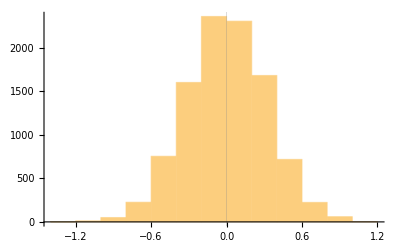

```mathematica
Histogram[means , GridLines->{{{Mean[dist1] , {Thick , Blue}}} , None},Method->{"GridLinesInFront"->True}]
```

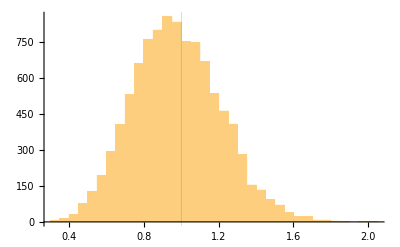

```mathematica
Histogram[stdvs , GridLines->{{{StandardDeviation[dist1] , {Thick , Blue}}} , None},Method->{"GridLinesInFront"->True}]
```

```mathematica
bsam = RandomVariate[dist1 , n]
```

{-2.2514,-0.592321,-0.0937045,-0.323315,0.0809759,-0.589565,-0.296958,-1.89425,-0.567411,1.15066}

```mathematica
bsample = Table[RandomChoice[bsam , n] , {b}];
```

```mathematica
bsample//Dimensions
```

{10000,10}

```mathematica
bmeans = Mean/@bsample;
```

```mathematica
bstdvs=StandardDeviation/@bsample;
```

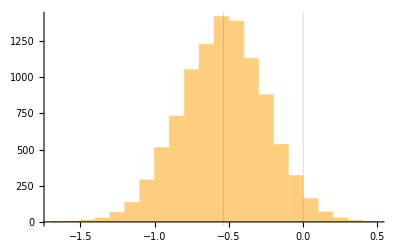

```mathematica
Histogram[bmeans , GridLines->{{{Mean[dist1] , {Thick , Blue}} , {Mean[bsam] , {Thick , Red}}} , None},Method->{"GridLinesInFront"->True}]
```

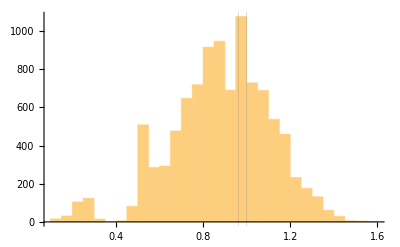

```mathematica
Histogram[bstdvs , GridLines->{{{StandardDeviation[dist1] , {Thick , Blue}} , {StandardDeviation[bsam] , {Thick , Red}}} , None},Method->{"GridLinesInFront"->True}]
```

```mathematica
StandardDeviation[means]
```

0.31791

```mathematica
StandardDeviation[bmeans]
```

0.28411

```mathematica
StandardDeviation[stdvs]
```

0.232301

```mathematica
StandardDeviation[bstdvs]
```

0.228688